# SEI2HR-Econ model with quarantine and supplies scenarios

## Version 0.7

Anton Antonov
MathematicaForPrediction at WordPress
SystemModeling at GitHub
March, April 2020

## Introduction

The epidemiology compartmental model, [Wk1], presented in this notebook -- SEI2HR-Econ -- deals with the all three rectangles in this diagram:

```mathematica
ImageResize[Import["https://github.com/antononcube/SystemModeling/raw/master/Projects/Coronavirus-propagation-dynamics/Diagrams/Coronavirus-propagation-simple-dynamics.jpeg"],900]
```

“SEI2HR” stands for “Susceptible, Exposed, Infected two, Hospitalized, Recovered” (populations.) “Econ” stands for “Economic”.

In this notebook we also deal with supplies scenarios. In the notebook [AA4] we deal with quarantine scenarios over a simpler model, SEI2HR.

Remark: We consider the contagious disease propagation models as instances of the more general System Dynamics (SD) models. We use SD terminology in this notebook.

### The models

#### SEI2R

The model SEI2R are introduced and explained in the notebook [AA2]. SEI2R differs from the classical SEIR model , [Wk1, HH1], with the following elements:

1. Two separate infected populations: one is "severely symptomatic", the other is "normally symptomatic"

2. The monetary equivalent of lost productivity due to infected or died people is tracked.

#### SEI2HR

For the formulation of SEI2HR we use a system of Differential Algebraic Equations (DAE’s). The package [AAp1] allows the use of a formulation that has just Ordinary Differential Equations (ODE’s).

Here are the unique features of SEI2HR:

People stocks

Two types of infected populations: normally symptomatic and severely symptomatic

Hospitalized population

Deceased from infection population

Hospital beds

Hospital beds are a limited resource that determines the number of hospitalized people

Only severely symptomatic people are hospitalized according to the available hospital beds

The hospital beds stock is not assumed constant, it has its own change rate.

Money stocks

The money from lost productivity are tracked

The money for hospital services are tracked

#### SEI2HR-Econ

SEI2HR-Econ adds the following features to SEI2HR:

Medical supplies

Medical supplies production

Medical supplies delivery

Medical supplies accumulation at hospitals

Medical supplies demand tracking

Hospitalization

Severely symptomatic people if according to two limited resources: hospital beds and medical supplies

Money stocks

Money for medical supplies production is tracked

#### SEI2HR-Econ’s place a development plan

This graph shows the “big picture” of the model development plan undertaken in [AAr1] and SEI2HR (discussed in this notebook) is in that graph:

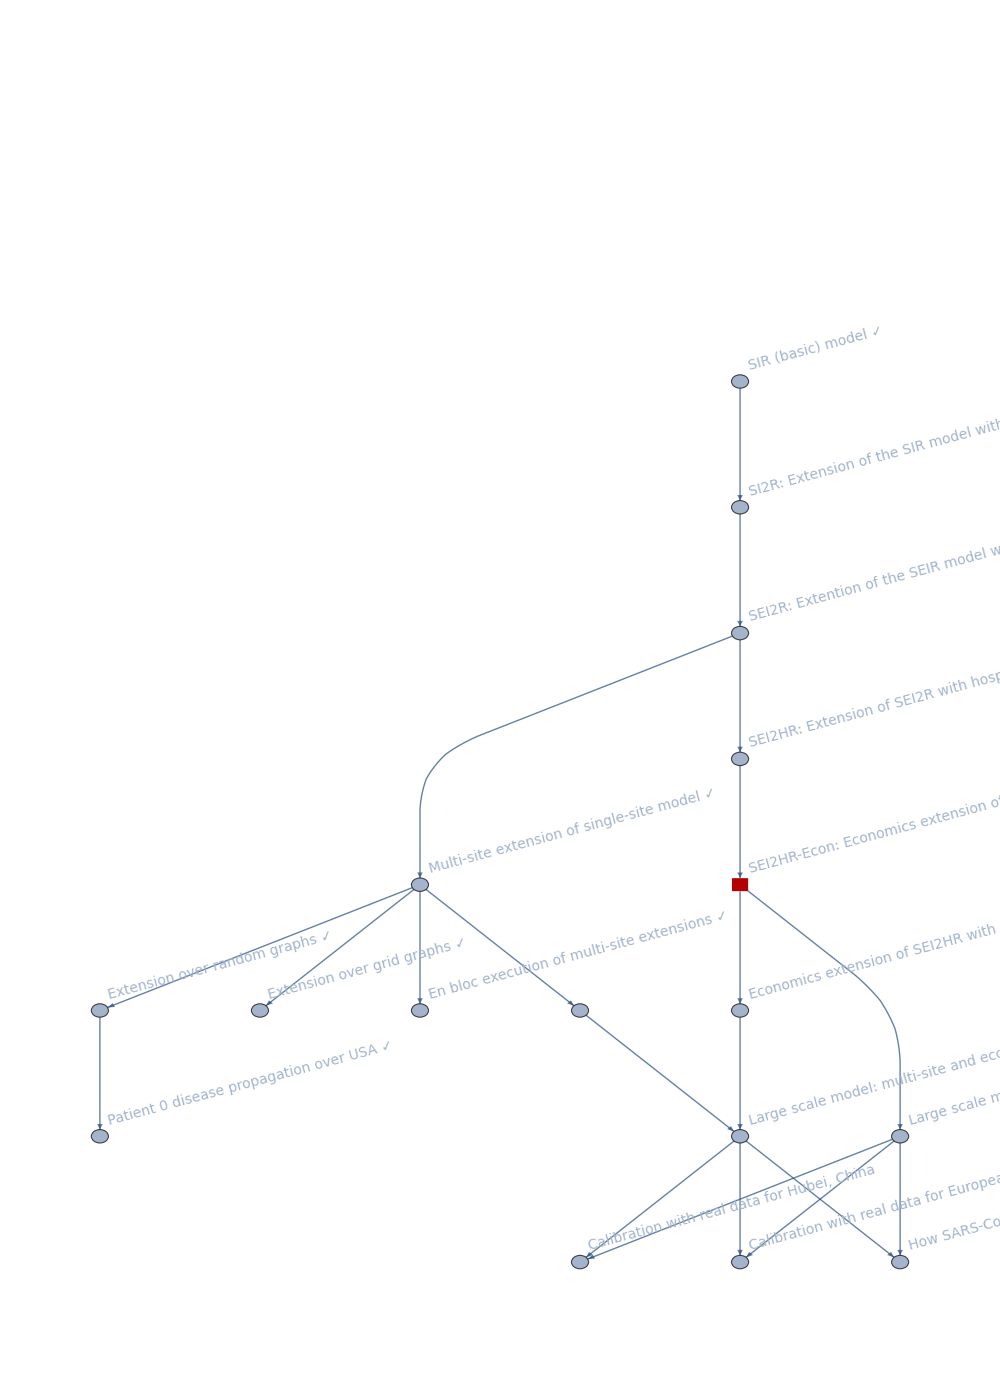

### Notebook structure

The rest of notebook has the following sequence of sections:

Package load section

SEI2HR-Econ structure in comparison of SEI2HR

Explanations of the equations of SEI2HR-Econ

Quarantine scenario modeling preparation

Medical supplies production and delivery scenario modeling preparation

Parameters and initial conditions setup

Populations, hospital beds, quarantine scenarios, medical supplies scenarios

Parametric simulation solution

Interactive interface

Sensitivity analysis

## Load packages

The epidemiological models framework used in this notebook is implemented with the packages [AAp1, AAp2, AA3]; many of the plot functions are from the package [AAp4].

```mathematica
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModels.m"];Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingSimulationFunctions.m"];Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
```

```mathematica
Get["/Volumes/Macintosh HD/Users/antonov/SystemModeling/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModels.m"]
```

## SEI2HR-Econ extends SEI2HR

The model SEI2HR-Econ is an extension of the model SEI2HR, [AA4].

Here is SEI2HR:

```mathematica
reprTP="AlgebraicEquation";
lsModelOpts={"Tooltips"->True,TooltipStyle->{Background->Yellow,CellFrameColor->Gray,FontSize->20}};
modelReference=SEI2HRModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->reprTP];
ModelGridTableForm[modelReference,lsModelOpts]
```

Here is SEI2HR-Econ:

```mathematica
modelSEI2HREcon=SEI2HREconModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->reprTP];
ModelGridTableForm[modelSEI2HREcon,lsModelOpts]
```

Here are the “differences” between the two models:

```mathematica
ModelGridTableForm@Merge[{modelSEI2HREcon,modelReference},If[AssociationQ[#⟦1⟧],KeyComplement[#],Complement@@#]&]
```

## Equations explanations

In this section we provide rationale of the model equations of SEI2HR-Econ.

The equations for Susceptible, Exposed, Infected, Recovered populations of SEI2R are "standard" and explanations about them are found in [WK1, HH1]. For SEI2HR those equations change because of the stocks Hospitalized Population and Hospital Beds. For SEI2HR-Econ the SEI2HR equations change because of the stocks Medical Supplies, Medical Supplies Demand, and Hospital Medical Supplies.

The equations time unit is one day. The time horizon is one year. Since we target COVID-19, [Wk2, AA1], we do not consider births.

Remark: For convenient reading the equations in this section have tooltips for the involved stocks and rates.

### Verbalization description of the model

We start with one infected (normally symptomatic) person, the rest of the people are susceptible. The infected people meet other people directly or get in contact with them indirectly. (Say, susceptible people touch things touched by infected.) For each susceptible person there is a probability to get the decease. The decease has an incubation period: before becoming infected the susceptible are (merely) exposed. The infected recover after a certain average infection period or die. A certain fraction of the infected become severely symptomatic. The severely symptomatic infected are hospitalized if there are enough hospital beds and enough medical supplies. The hospitalized severely infected have different death rate than the non-hospitalized ones. The number of hospital beds might change: hospitals are extended, new hospitals are build, or there are not enough medical personnel or supplies. The medical supplies are produced with a certain rate and delivered after a certain delay period. The hospitals have their own stock of medical supplies. The combined demand from all populations for medical supplies is tracked. The deaths from infection are tracked (accumulated.) Money for medical supplies production, money for hospital services, and money from lost productivity are tracked (accumulated.)

The equations below give mathematical interpretation of the model description above.

The equations descriptions are not finished in this notebook version.

### Code for the equations

Each equation in this section are derived with code like this:

```mathematica
ModelGridTableForm[modelSEI2HREcon, lsModelOpts]["Equations"][[1, EquationPosition[modelSEI2HREcon, RP] + 1, 2]]
```

and then the output cell is edited to be “DisplayFormula” and have CellLabel value corresponding to the stock of interest.

### The infected and hospitalized populations

SEI2HR has two types of infected populations: a normally symptomatic one and a severely symptomatic one. A major assumption for SEI2HR is that only the severely symptomatic people are hospitalized. (That assumption is also reflected in the diagram in the introduction.)

Each of those three populations have their own contact rates and mortality rates.

Here are the contact rates from the SEI2HR-Econ dictionary

```mathematica
ColumnForm@Cases[Normal@modelSEI2HREcon["Rates"],HoldPattern[β[_]->_],∞]
```

Here are the mortality rates from the SEI2HR-Econ dictionary

```mathematica
ColumnForm@Cases[Normal@modelSEI2HREcon["Rates"],HoldPattern[μ[_]->_],∞]
```

Remark: Below with “Infected Population” we mean both stocks Infected Normally Symptomatic Population (INSP) and Infected Severely Symptomatic Population (ISSP).

### Total Population

In this notebook we consider a DAE’s formulation of SEI2HR-Econ. The stock Total Population has the following (obvious) algebraic equation:

```mathematica
ModelGridTableForm[modelSEI2HREcon,lsModelOpts]["Equations"]⟦1,EquationPosition[modelSEI2HREcon,TP]+1,2⟧
```

TP[t]==Max[0,EP[t]+INSP[t]+ISSP[t]+RP[t]+SP[t]]

Note that with Max we specified that the total population cannot be less than 0.

Remark: As mentioned in the introduction, the package [AAp1] allows for the use of non-algebraic formulation, without an equation for TP.

### Susceptible Population

The stock Susceptible Population (SP) is decreased by (1) infections derived from stocks Infected Populations and Hospitalized Population (HP), and (2) morality cases derived with the typical mortality rate.

SP'[t]==-(HP[t] SP[t] β[HP])/TP[t]-(INSP[t] SP[t] β[INSP])/TP[t]-(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t]-SP[t] μ[TP]

Because we hospitalize the severely infected people only instead of the term

(ISSP[t]SP[t]β[ISSP])/TP[t]

we have the terms

(HP[t] SP[t] β[HP])/TP[t]+(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t].

The first term is for the infections derived from the hospitalized population. The second term for the infections derived from people who are infected severely symptomatic and not hospitalized.

#### Births term

Note that we do not consider in this notebook births, but the births term can be included in SP’s equation:

```mathematica
Block[{m=SEI2HREconModel[t,"BirthsTerm"->True]},
ModelGridTableForm[m]["Equations"]⟦1,EquationPosition[m,SP]+1,2⟧
]
```

The births rate is the same as the death rate, but it can be programmatically changed. (See [AAp2].)

### Exposed Population

The stock Exposed Population (EP) is increased by (1) infections derived from the stocks Infected Populations and Hospitalized Population, and (2) mortality cases derived with the typical mortality rate. EP is decreased by (1) the people who after a certain average incubation period (aincp) become ill, and (2) mortality cases derived with the typical mortality rate.

EP'[t]==(HP[t] SP[t] β[HP])/TP[t]+(INSP[t] SP[t] β[INSP])/TP[t]+(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t]-EP[t] (1/aincp+μ[TP])

### Infected Normally Symptomatic Population

INSP is increased by a fraction of the people who have been exposed. That fraction is derived with the parameter severely symptomatic population fraction (sspf). INSP is decreased by (1) the people who recover after a certain average infection period (aip), and (2) the normally symptomatic people who die from the disease.

INSP'[t]==-INSP[t]/aip+(EP[t] (1-sspf[SP]))/aincp-INSP[t] μ[INSP]

### Infected Severely Symptomatic Population

ISSP is increased by a fraction of the people who have been exposed. That fraction is corresponds to the parameter severely symptomatic population fraction (sspf). ISSP is decreased by (1) the people who recover after a certain average infection period (aip), (2) the hospitalized severely symptomatic people who die from the disease, and (3) the non-hospitalized severely symptomatic people who die from the disease.

ISSP'[t]==-ISSP[t]/aip+(EP[t] sspf[SP])/aincp-HP[t] μ[HP]-(-HP[t]+ISSP[t]) μ[ISSP]

Note that we do not assume that severely symptomatic people recover faster if they are hospitalized, only that they have a different death rate.

### Hospitalized Population

The amount of people that can be hospitalized is determined by the available Hospital Beds (HB) -- the stock Hospitalized Population (HP) is subject to a resource limitation by the stock HB.

The equation of the stock HP can be easily understood from the following dynamics description points:

If the number of hospitalized people is less that the number of hospital beds we hospitalize the new ISSP people.

The Available Hospital Beds (AHB) are determined by the minimum of (i) the non-occupied hospital beds, and (ii) the hospital medical supplies divided by the ISSP consumption rate.

If the new ISSP people are more than AHB we take as many as AHB.

Hospitalized people have the same average infection period (aip).

Hospitalized (severely symptomatic) people have their own mortality rate.

Here is the HP equation:

HP'[t]==(Piecewise[{{Min[HB[t]-HP[t],HMS[t]/mscr[ISSP],(EP[t] sspf[SP])/aincp], HP[t]<HB[t]}, {0, True}}])-HP[t]/aip-HP[t] μ[HP]

Note that although we know that in a given day some hospital beds are going to be freed they are not considered in the hospitalization plans for that day. Similarly, we know that new medical supplies are coming but we do not include them into AHB.

### Recovered Population

The stock Recovered Population (RP) is increased by the recovered infected people and decreased by mortality cases derived with the typical mortality rate.

RP'[t]==(INSP[t]+ISSP[t])/aip-RP[t] μ[TP]

### Deceased Infected Population

The stock Deceased Infected Population (DIP) accumulates the deaths of the people who are infected. Note that we utilize the different death rates for HP and ISSP.

DIP'[t]==HP[t] μ[HP]+INSP[t] μ[INSP]+(-HP[t]+ISSP[t]) μ[ISSP]

### Hospital Beds

The stock Hospital Beds (HB) can change with a rate that reflects the number of hospital beds change rate (nhbcr) per day. Generally speaking, using nhbcr we can capture scenarios, like, extending hospitals, building new hospitals, recruitment of new medical personnel, loss of medical personnel (due to infections.)

HB'[t]==HB[t] nhbcr[ISSP,INSP]

### Hospital Medical Supplies

The Hospital Medical Supplies (HMS) are decreased according to the medical supplies consumption rate (mscr) of HP and increased by a Medical Supplies (MS) delivery term (to be described next.)

The MS delivery term is build with the following assumptions / postulates:

Every day the hospital attempts to order MS that correspond to HB multiplied by mscr.

The hospital has limited capacity of MS storage, κ[HMS].

The MS producer has limited capacity for delivery, κ[MDS].

The hospital demand for MS has precedence over the demands for the non-hospitalized populations.

Hence, if the MS producer has less stock of MS than the demand of the hospital that whole amount of MS goes to the hospital.

The supplies are delivered with some delay period: the medical supplies delivery period (msdp).

Here is the MS delivery term:

Min[MS[t],κ[MSD],HB[t] mscr[ISSP],κ[HMS]-HMS[t]]/msdp[HB]

Here is the corresponding HMS equation:

HMS'[t]==-Min[HMS[t],HP[t] mscr[ISSP]]+Min[MS[t],HB[t] mscr[ISSP],-HMS[t]+κ[HMS],κ[MSD]]/msdp[HB]

### Medical Supplies

The equation of the Medical Supplies (MS) stock is based on the following assumptions / postulates:

The non-hospitalized people go to the MS producer to buy supplies. (I.e. only delivery to the hospital.)

The MS producer vehicles have certain capacity, κ[MSD].

The MS producer has a certain storage capacity (for MS stock.)

Each of INSP, ISSP, and HP has its own specific medical supplies consumption rate (mscr). EP, RP, and TP have the same mscr.

The hospital has precedence in its MS order. I.e. the demand from the hospital is satisfied first, and then for the rest of the populations.

Here is the MS delivery term described in the previous section:

```mathematica
dlvr=Min[MS[t],κ[MSD],HB[t] mscr[HP],κ[HMS]-HMS[t]]/msdp[HB];
```

Here is the MS formula with the MS delivery term replaced with “Dlvr”:

```mathematica
ModelGridTableForm[modelSEI2HREcon,"Tooltips"->False]["Equations"]⟦1,EquationPosition[modelSEI2HREcon,MS]+1,2⟧/.dlvr->Dlvr
```

We can see from that equation that MS is increased by medical supplies production rate (mspr) with dimension number of units per day. The production is restricted by the storage capacity, κ[MS]:

Min[mspr[HB], -MS[t] + κ[MS]]

MS is decreased by the MS delivery term and the demand from the non-hospitalized populations. Because the hospital has precedence, we use in the equation:

Min[-Dlvr+MS[t],"non-hospital demand"]

Here is the full MS equation:

MS'[t]==-Min[MS[t]-Min[MS[t],HB[t] mscr[HP],-HMS[t]+κ[HMS],κ[MSD]]/msdp[HB],INSP[t] mscr[INSP]+(-HP[t]+ISSP[t]) mscr[INSP]+mscr[TP] (EP[t]+RP[t]+SP[t])]+Min[mspr[HB],-MS[t]+κ[MS]]-Min[MS[t],HB[t] mscr[HP],-HMS[t]+κ[HMS],κ[MSD]]/msdp[HB]

### Medical Supplies Demand

The stock Medical Supplies Demand (MSD) simply accumulates the MS demand derived from population stocks and their corresponding mscr:

MSD'[t]==INSP[t] mscr[INSP]+ISSP[t] mscr[ISSP]+mscr[TP] (EP[t]+RP[t]+SP[t])

### Money for Hospital Services

The stock Money for Hospital Services (MHS) simply tracks expenses for hospitalized people. The parameter hospital services cost rate (hscr) with unit money per bed per day simply multiplies HP.

MHS'[t]==HP[t] hscr[ISSP,INSP]

### Money from Lost Productivity

The stock Money from Lost Productivity (MLP) simply tracks the work non-availability of the infected and died from infection people. The parameter lost productivity cost rate (lpcr) with unit money per person per day multiplies the total count of the infected and dead from infection.

MLP'[t]==lpcr[ISSP,INSP] (INSP[t]+ISSP[t]+HP[t] μ[HP]+INSP[t] μ[INSP]+(-HP[t]+ISSP[t]) μ[ISSP])

## Quarantine scenarios

In order to model quarantine scenarios we use piecewise constant functions for the contact rates β[ISSP] and β[INSP].

Remark: Other functions can be used, like, functions derived through some statistical fitting.

Here is an example plot :

```mathematica
Block[{func=β*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1]},
Legended[
Block[{β=0.56,qsd=60,ql=8*7,qcrf=0.25},
ListLinePlot[Table[func,{t,0,365}],PlotStyle->"Detailed"]
],func]]
```

To model quarantine with a piecewise constant function we use the following  parameters:

qsd for quarantine's start

ql for quarantines duration

qcrf for the effect on the quarantine on the contact rate

## Medical supplies scenarios

We consider three main scenarios for the medical supplies:

Constant production rate and consistent delivery (constant delivery period)

Constant production rate and disrupted delivery

Disrupted production and disrupted delivery

The disruptions are simulated with simple pulse functions -- we want to see how the system being modeled reacts to singular, elementary disruption.

Here is an example plot of a disruption of delivery period plot :

```mathematica
Block[{func=bp*Piecewise[{{1,t<ds},{sf,ds≤t≤ds+dl}},1]},
Legended[
Block[{bp=1,ds=70,dl=1,sf=1.8},
ListLinePlot[Table[func,{t,0,365}],PlotStyle->"Detailed"]
],func]]
```

To model disruption of delivery with a piecewise constant function we use the following  parameters:

bp for the base delivery period

ds for disruption start

dl for disruption duration

sf for how much slower or faster the delivery period becomes

To be finished...

## Parameters and actual simulation equations code

Here are the parameters we want to experiment with (or do calibration with):

```mathematica
lsFocusParams={aincp,aip,sspf[SP],β[HP],qsd,ql,qcrf,nhbcr[ISSP,INSP],nhbr[TP],mspr[HB],msdp[HB]};
```

Here we set custom rates and initial conditions:

```mathematica
population=10^6;
If[reprTP=="AlgebraicEquation",
modelSEI2HREcon=SetRateRules[modelSEI2HREcon,
<|
TP[0]->population,
β[ISSP]->0.5*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
β[INSP]->0.5*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
qsd->60,
ql->8*7,
qcrf->0.25,
β[HP]->0.01,
μ[ISSP]->0.035/aip,
μ[INSP]->0.01/aip,
nhbr[TP]->3/1000,
lpcr[ISSP,INSP]->1,
hscr[ISSP,INSP]->1
|>];
modelSEI2HREcon=SetInitialConditions[modelSEI2HREcon,<|TP[0]==population,SP[0]->population-1,ISSP[0]->0,INSP[0]->1|>],
(*ELSE*)
modelSEI2HREcon=SetRateRules[modelSEI2HREcon,<|TP[t]->population,β[ISSP]->0.56,β[INSP]->0.56,β[HP]->0.01,μ[ISSP]->0.035/aip,μ[INSP]->0.01/aip,μ[HP]->0.005/aip,nhbr[TP]->population*3/1000|>];modelSEI2HREcon=SetInitialConditions[modelSEI2HREcon,<|SP[0]->population-1,ISSP[0]->0,INSP[0]->1|>];
];
```

Remark: Note the piecewise functions for β[ISSP] and β[INSP].

Here is the system of ODE’s we use to do parametrized simulations:

```mathematica
lsActualEquations=ModelNDSolveEquations[modelSEI2HREcon,KeyDrop[modelSEI2HREcon["RateRules"],lsFocusParams]];
ResourceFunction["GridTableForm"][List/@lsActualEquations]
```

## Simulation

### Solutions

Straightforward simulation for one year using ParametricNDSolve :

```mathematica
aParSol=
Association@Flatten@
ParametricNDSolve[lsActualEquations,GetStockSymbols[modelSEI2HREcon,__~~__],{t,0,365},lsFocusParams];
```

### Example evaluation

Here are the parameters of a stock solution:

```mathematica
aParSol[HP]
```

```mathematica
aSol[HP]["Parameters"]
```

```mathematica
aAllRules=Join[Association[Rule@@@modelSEI2HREcon["InitialConditions"]],modelSEI2HREcon["RateRules"]];
```

Here we replace the parameters with concrete rate values (kept in the model object):

```mathematica
aParSol[HP]["Parameters"]//.aAllRules
```

Here is an example evaluation of a solution using the parameter values above:

```mathematica
With[{seq=Sequence@@(aParSol[HP]["Parameters"]//.aAllRules)},aParSol[HP][seq][100]]
```

## Interactive interface

Using the interface in this section we can interactively see the effects of changing the focus parameters.

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->400};
lsPopulationKeys={TP,SP,EP,ISSP,INSP,HP,RP,DIP,HB};
lsSuppliesKeys={MS,MSD,HMS};
lsMoneyKeys={MHS,MLP,MMSP};
Manipulate[
DynamicModule[{aStocks=modelSEI2HREcon["Stocks"],aSolLocal=aParSol,lsPopulationPlots,lsMoneyPlots,lsSuppliesPlots},

lsPopulationPlots=
Quiet@ParametricSolutionsPlots[
aStocks,
KeyTake[aSolLocal,Intersection[lsPopulationKeys,displayPopulationStocks]],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000,mspr,msdp},ndays,
"LogPlot"->popLogPlotQ,"Together"->popTogetherQ,"Derivatives"->popDerivativesQ,"DerivativePrefix"->"Δ",opts];

lsSuppliesPlots=
If[Length[KeyDrop[aSolLocal,Join[lsPopulationKeys,lsMoneyKeys]]]==0,{},
(*ELSE*)
Quiet@ParametricSolutionsPlots[
aStocks,
KeyTake[KeyDrop[aSolLocal,Join[lsPopulationKeys,lsMoneyKeys]],displaySupplyStocks],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000,mspr,msdp},ndays,
"LogPlot"->supplLogPlotQ,"Together"->supplTogetherQ,"Derivatives"->supplDerivativesQ,"DerivativePrefix"->"Δ",opts]
];

lsMoneyPlots=
Quiet@ParametricSolutionsPlots[
aStocks,
KeyTake[aSolLocal,Intersection[lsMoneyKeys,displayMoneyStocks]],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000,mspr,msdp},ndays,
"LogPlot"->moneyLogPlotQ,"Together"->moneyTogetherQ,"Derivatives"->moneyDerivativesQ,"DerivativePrefix"->"Δ",opts];

Multicolumn[Join[lsPopulationPlots,lsSuppliesPlots,lsMoneyPlots],nPlotColumns,Dividers->All,FrameStyle->GrayLevel[0.8]],
SaveDefinitions->True
],
{{ndays,365,"Number of days"},1,365,1,Appearance->{"Open"}},
Delimiter,
{{aincp,6.,"Average incubation period (days)"},1,60.,1,Appearance->{"Open"}},
{{aip,21.,"Average infectious period (days)"},1,60.,1,Appearance->{"Open"}},
{{spf,0.2,"Severely symptomatic population fraction"},0,1,0.025,Appearance->{"Open"}},
{{crhp,0.1,"Contact rate of the hospitalized population"},0,30,0.1,Appearance->{"Open"}},
Delimiter,
{{qsd,65,"Quarantine start days"},0,365,0.01,Appearance->{"Open"}},
{{ql,8*7,"Quarantine length (in days)"},0,120,1,Appearance->{"Open"}},
{{qcrf,0.25,"Quarantine contact rate fraction"},0,1,0.01,Appearance->{"Open"}},
Delimiter,
{{nhbr,2.9,"Number of hospital beds rate (per 1000 people)"},0,100,0.1,Appearance->{"Open"}},
{{nhbcr,0,"Number of hospital beds change rate"},-0.5,0.5,0.001,Appearance->{"Open"}},
{{mspr,200,"Medical supplies production rate"},0,50000,10,Appearance->{"Open"}},
{{msdp,1.2,"Medical supplies delivery period"},0,10,0.1,Appearance->{"Open"}},
Delimiter,
{{displayPopulationStocks,lsPopulationKeys,"Population stocks to display:"},lsPopulationKeys,ControlType->TogglerBar},
{{popTogetherQ,True,"Plot populations together"},{False,True}},
{{popDerivativesQ,False,"Plot populations derivatives"},{False,True}},
{{popLogPlotQ,False,"LogPlot populations"},{False,True}},
Delimiter,
{{displaySupplyStocks,lsSuppliesKeys,"Supplies stocks to display:"},lsSuppliesKeys,ControlType->TogglerBar},
{{supplTogetherQ,True,"Plot supplies functions together"},{False,True}},
{{supplDerivativesQ,False,"Plot supplies functions derivatives"},{False,True}},
{{supplLogPlotQ,True,"LogPlot supplies functions"},{False,True}},
Delimiter,
{{displayMoneyStocks,lsMoneyKeys,"Money stocks to display:"},lsMoneyKeys,ControlType->TogglerBar},
{{moneyTogetherQ,True,"Plot money functions together"},{False,True}},
{{moneyDerivativesQ,False,"Plot money functions derivatives"},{False,True}},
{{moneyLogPlotQ,True,"LogPlot money functions"},{False,True}},
{{nPlotColumns,1,"Number of plot columns"},Range[5]},
ControlPlacement->Left,ContinuousAction->False]
```

## Sensitivity analysis

When making and using this kind of dynamics models it is important to see how the solutions react to changes of different parameters. For example, we should try to find answers to questions like "What ranges of which parameters bring dramatic changes into important stocks?"

Sensitivity Analysis (SA) is used to determine how sensitive is a SD model to changes of the parameters and to changes of model’s equations, [BC1]. More specifically, parameter sensitivity, which we apply below, allows us to see the changes of stocks dynamic behaviour for different sequences (and combinations) of parameter values.

Remark: This section to mirrors to a point the section with same name in [AA4], except in this notebook we are more interested in medical supplies related SA because quarantine related SA is done in [AA4].

Remark: SA shown below should be done for other stocks and rates. In order to keep this exposition short we focus on ISSP, DIP, and HP. Also, it is interesting to think in terms of “3D parameter sensitivity plots.” We also do such plots.

### Evaluations by Area under the curve

For certain stocks we might be not just interested in their evolution in time but also in their cumulative values. I.e. we are interested in the so called Area Under the Curve (AUC) metric for those stocks.

There are three ways to calculate AUC for stocks of interest:

Add aggregation equations in the system of ODE’s. (Similar to the stock DIP in SEI2HR.)

For example, in order to compute AUC for ISSP we can add to SEI2HR the equation:

aucISSP'[t]=ISSP[t]

More details for such equation addition are given in [AA2].

Apply NIntegrate over stocks solution functions.

Apply Trapezoidal rule to stock solution function values over a certain time grid.

Below we use 1 and 3.

### Variation of medical supplies delivery period

Here are calculate the solutions for a certain combination of capacities and rates:

```mathematica
AbsoluteTiming[
aVarSolutions=
Association@
Map[
Function[{msdpVar},
model2=SEI2HREconModel[t];
model2=SetRateRules[model2,<|κ[MS]->10000,κ[HMS]->100,mspr[HB]->100,msdp[HB]->msdpVar|>];
msdpVar->Association[ModelNDSolve[model2,{t,365}]⟦1⟧]
],
Union[Join[Range[0.2,1,0.2],Range[1,3,0.5]]]
];
]
```

As expected more frequent delivery results in fuller utilization of the non-occupied hospital beds:

```mathematica
SeedRandom[23532]
aVals=#[HP][Range[0,365]]&/@aVarSolutions;
ListLinePlot[KeyValueMap[Callout[#2,#1,{If[#1<1,RandomInteger[{120,150}],RandomInteger[{160,260}]],Above}]&,aVals],PlotLegends->Keys[aVals],PlotRange->All,ImageSize->Large,PlotLabel->"Hospitalized Population"]
```

Here are the corresponding AUC values:

```mathematica
aAUCs=TrapezoidalRule[Transpose[{Range[0,365],#}]]&/@aVals;
ResourceFunction["GridTableForm"][aAUCs]
```

```mathematica
BarChart[aAUCs,ChartLabels->Keys[aAUCs],ColorFunction->"Pastel",PlotLabel->"Hospitalized Population AUC"]
```

### Variation of medical supplies production rate

In order to demonstrate the effect of medical supplies production rate (mspr) it is beneficial to eliminate the number of hospital beds restriction -- we assume that we have enough hospital beds for severely symptomatic people.

Here are calculate the solutions for a certain combination of capacities and rates:

```mathematica
AbsoluteTiming[
aVarSolutions=
Association@
Map[
Function[{msprVar},
model2=SEI2HREconModel[t];
model2=SetRateRules[model2,<|κ[MS]->100000,κ[HMS]->10000,κ[MSD]->10000,mspr[HB]->msprVar,msdp[HB]->1.5,mscr[ISSP]->0.2,mscr[TP]->0.001,mscr[ISSP]->1,nhbr[TP]->100/1000|>];
msprVar->Association[ModelNDSolve[model2,{t,365}]⟦1⟧]
],
{20,60,100,200,300,1000,10000}
];
]
```

#### Hospitalized Population

As expected we can see that with smaller production rate we get less hospitalized people:

```mathematica
SeedRandom[1232]
aVals=#[HP][Range[0,365]]&/@aVarSolutions;
ListLinePlot[KeyValueMap[Callout[#2,#1,{RandomInteger[{180,240}],Above}]&,aVals],PlotLegends->Keys[aVals],PlotRange->All,ImageSize->Large,PlotLabel->"Hospitalized Population"]
```

Here are the corresponding AUC values:

```mathematica
aAUCs=TrapezoidalRule[Transpose[{Range[0,365],#}]]&/@aVals;
ResourceFunction["GridTableForm"][aAUCs]
```

```mathematica
BarChart[aAUCs,ChartLabels->Keys[aAUCs],ColorFunction->"Pastel",PlotLabel->"Hospitalized Population AUC"]
```

#### Medical Supplies

Here we plot the availability of MS at MS producer’s storage:

```mathematica
SeedRandom[821]
aVals=#[MS][Range[0,365]]&/@aVarSolutions;
ListLinePlot[KeyValueMap[Callout[#2,#1,{RandomInteger[{100,160}],Above}]&,aVals],PlotLegends->Keys[aVals],PlotRange->All,ImageSize->Large,PlotLabel->"Medical Supplies"]
```

Here are the corresponding AUC values:

```mathematica
aAUCs=TrapezoidalRule[Transpose[{Range[0,365],#}]]&/@aVals;
ResourceFunction["GridTableForm"][aAUCs]
```

```mathematica
BarChart[aAUCs,ChartLabels->Keys[aAUCs],ColorFunction->"Pastel",PlotLabel->"Medical Supplies AUC"]
```

## References

### Articles

[Wk1] Wikipedia entry, "Compartmental models in epidemiology".

[Wl2] Wikipedia entry, "Coronavirus disease 2019".

[HH1] Herbert W. Hethcote (2000). "The Mathematics of Infectious Diseases". SIAM Review. 42 (4): 599–653. Bibcode:2000SIAMR..42..599H. doi:10.1137/s0036144500371907.

[BC1] Lucia Breierova,  Mark Choudhari,  An Introduction to Sensitivity Analysis, (1996), Massachusetts Institute of Technology.

[AA1] Anton Antonov, "Coronavirus propagation modeling considerations", (2020), SystemModeling at GitHub.

[AA2] Anton Antonov, "Basic experiments workflow for simple epidemiological models", (2020), SystemModeling at GitHub.

[AA3] Anton Antonov, "Scaling of Epidemiology Models with Multi-site Compartments", (2020), SystemModeling at GitHub.

[AA4] Anton Antonov, "SEI2HR model with quarantine scenarios", (2020), SystemModeling at GitHub.

### Repositories, packages

[WRI1] Wolfram Research, Inc., "Epidemic Data for Novel Coronavirus COVID-19", WolframCloud.

[AAr1] Anton Antonov, Coronavirus propagation dynamics project, (2020), SystemModeling at GitHub.

[AAp1] Anton Antonov, "Epidemiology models Mathematica package", (2020), SystemsModeling at GitHub.

[AAp2] Anton Antonov, "Epidemiology models modifications Mathematica package", (2020), SystemsModeling at GitHub.

[AAp3] Anton Antonov, "Epidemiology modeling visualization functions Mathematica package", (2020), SystemsModeling at GitHub.

[AAp4] Anton Antonov, "System dynamics interactive interfaces functions Mathematica package", (2020), SystemsModeling at GitHub.

### Project management files

[AAo1] Anton Antonov, WirVsVirus-Hackathon-work-plan.org, (2020), SystemsModeling at GitHub.

[AAo2] Anton Antonov, WirVsVirus-hackathon-Geo-spatial-temporal-model-mind-map, (2020), SystemsModeling at GitHub.